```mathematica
Dens[en_]=FourierTransform[(BesselJ[0,t/2])^2/Sqrt[2Pi],t,en,Assumptions->en>-1&&en<1]
```

(2 EllipticK[1-en^2])/π^2

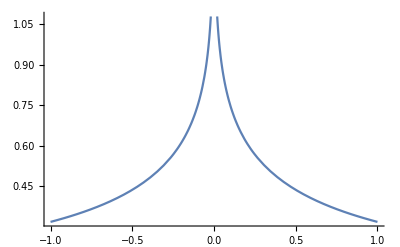

```mathematica
Plot[Dens[x],{x,-1,1}]
```

```mathematica
Denstab={N@#,N@Dens[#]}&/@Table[i/1000,{i,-10000,10000}]
```

{{-10.,0.0748893},{-9.999,0.0748948},{-9.998,0.0749002},{-9.997,0.0749057},{-9.996,0.0749112},{-9.995,0.0749167},{-9.994,0.0749222},{-9.993,0.0749277},{-9.992,0.0749332},{-9.991,0.0749387},19981,{9.991,0.0749387},{9.992,0.0749332},{9.993,0.0749277},{9.994,0.0749222},{9.995,0.0749167},{9.996,0.0749112},{9.997,0.0749057},{9.998,0.0749002},{9.999,0.0748948},{10.,0.0748893}}
 |  |  |  |

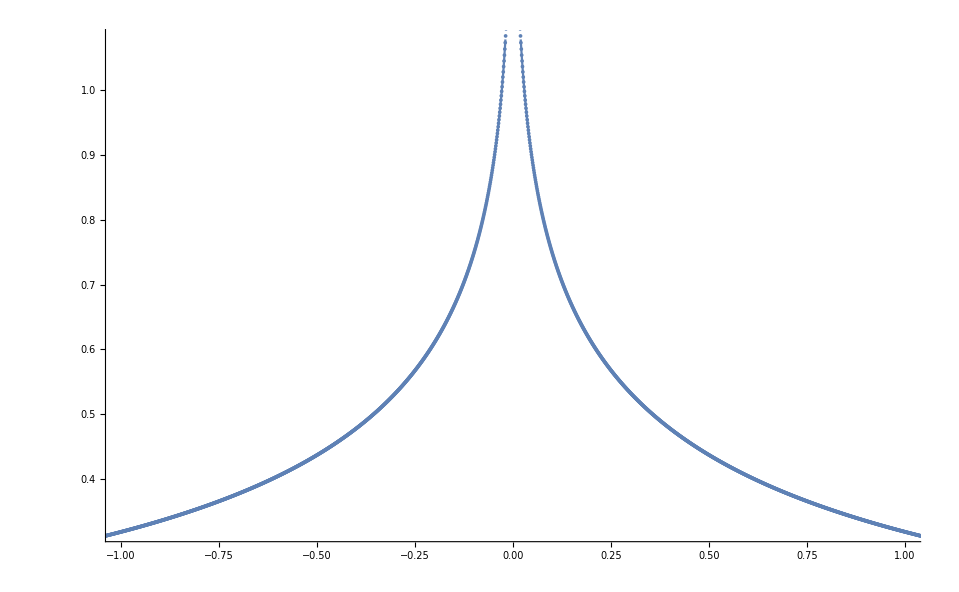

```mathematica
Show[{Plot[Dens[x],{x,-1,1}],ListPlot[Denstab]}]
```

```mathematica
Export["dens2d.dat",Denstab]
```

dens2d.dat

```mathematica
ekin[beta_]:=NIntegrate[2.0*Dens[x]*x/(Exp[x*beta]+1),{x,-1,1}]
```

```mathematica
betatab={13.0,14.0,15.6,17.4,19.6,22.4,26.1,32.4,39.4,52.8,65.0,80.0}
```

{13.,14.,15.6,17.4,19.6,22.4,26.1,32.4,39.4,52.8,65.,80.}

```mathematica
ekintab={#,ekin[#]}&/@Table[100000.0/i,{i,1,10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{100000.,-0.405285},{50000.,-0.405285},{33333.3,-0.405285},{25000.,-0.405285},{20000.,-0.405285},{16666.7,-0.405285},{14285.7,-0.405285},{12500.,-0.405285},9984,{10.007,-0.384188},{10.006,-0.384185},{10.005,-0.384181},{10.004,-0.384178},{10.003,-0.384174},{10.002,-0.38417},{10.001,-0.384167},{10.,-0.384163}}
 |  |  |  |

```mathematica
Export["EkinU0.dat",ekintab]
```

EkinU0.dat

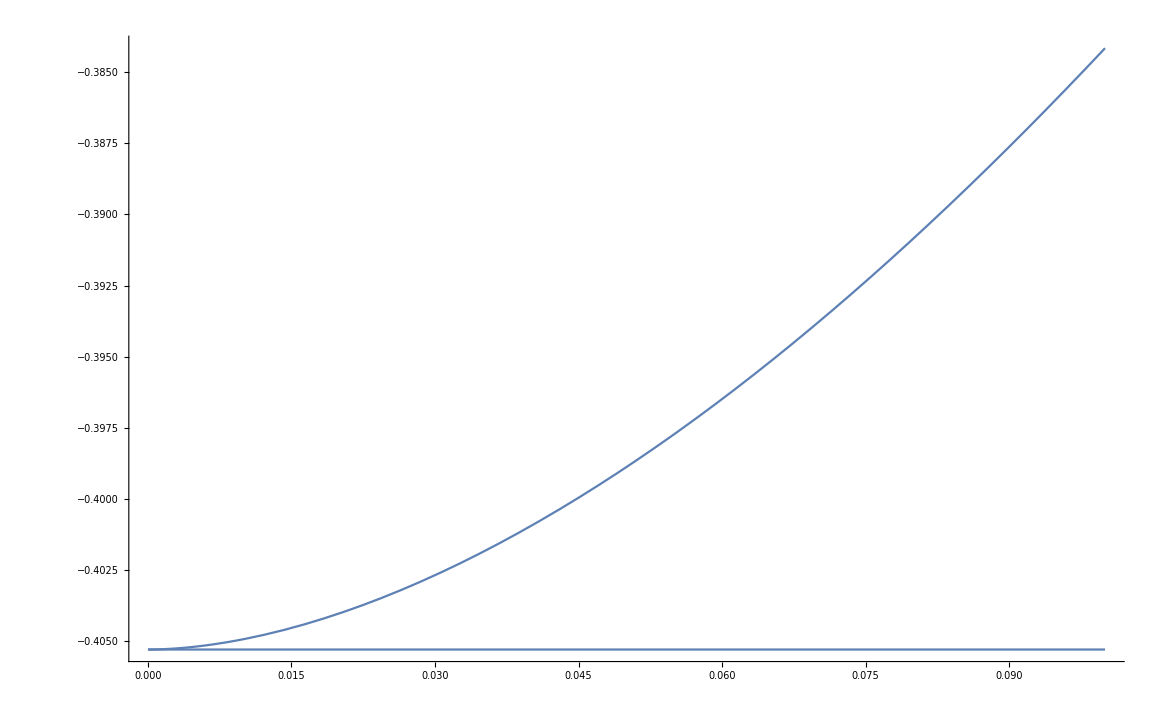

```mathematica
Show[Plot[ekin[1/x],{x,0.00001,0.1}],ListPlot[ekintab,Joined->True],Plot[-4/Pi^2,{x,0.00001,0.1}]]
```

```mathematica
occup[beta_,en_]=Dens[en]/(Exp[beta*en]+1)
```

(4 EllipticK[1-en^2])/((1+ⅇ^(beta en)) π^2)

```mathematica
occup1[beta_]:=({N@#1,N@occup[beta,#1]}&/@Table[i/10000,{i,-10000,10000}])
```

```mathematica
Export["occup_beta"<>ToString[#]<>"0.dat",occup1[#]]&/@betatab
```

{occup_beta26.0.dat,occup_beta27.0.dat,occup_beta28.0.dat,occup_beta29.0.dat,occup_beta30.0.dat,occup_beta31.0.dat,occup_beta32.0.dat,occup_beta33.0.dat,occup_beta34.0.dat,occup_beta35.0.dat,occup_beta40.0.dat,occup_beta60.0.dat,occup_beta80.0.dat}

```mathematica
Integrate[2*Dens[x]*x,{x,-1,0}]
```

-4/π^2

```mathematica
beta1tab:=Table[i,{i,26,1000}]
```

```mathematica
ekin1tab:={#,ekin[#]}&/@beta1tab
```

```mathematica
Export["Ekin1U0.dat",ekin1tab]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

Ekin1U0.dat